# Uniswap V3 Pricing Review for Lenders

## Abstract

With the creation of Uniswap, thorough stochastic pricing analysis has been reviewed by Bardoscia and Milionis describing it’s spot pricing dynamics. Since it’s release, only a few protocols have been created to address leveraged perpetual options using Uniswap V3 pricing dynamics, effectively creating a “loan” based on backed collateral for position holders. Below is a review of simulation using Mathematica to generate empirical risk profiles for V3 positions with standard techniques in Stochastic Calculus.

## Stochastic Calculus Review

## Ito’s Lemma

### Single Variable Ito’s Lemma

-Graphics-

```mathematica
SVIto[F_, var_, stocs_] := Sum[ i[[2]] * D[F, var] * ⅆi[[1]], {i, {{t, α}, {W, β}}}] + 
1/2 β^2*D [F, {var, 2}] * ⅆt /. stocs // Simplify
```

### Multivariable Ito’s Lemma

-Graphics-

```mathematica
MVIto[F_, vars_, stocs_] := 
Sum[ D[F, {var}] * ⅆvar, {var, vars}] + 
Sum[  1/2 D [F, pairs[[1]], pairs[[2]]] * ⅆpairs[[1]] * ⅆpairs[[2]],{pairs, Subsets[vars, {2}] ~Join~ Map[{#, #}&,vars]}]  /. stocs // Simplify;
```

### Sanity Checks

The Single Variable Ito should correctly return GBM.

```mathematica
SVIto @@ {ⅇ^S, S, {ⅆS -> μ  ⅆt + σ  ⅆW, α -> μ , β -> σ} }  // (#/ⅇ^S)& // Simplify
```

(μ+σ^2/2) ⅆt+σ ⅆW

The Multi-variable Ito should correctly return the Forward Contract process.

```mathematica
MVIto@@{ S*ⅇ^(y(T-t)), {S, t},{ⅆS -> μ S ⅆt + σ S ⅆW} }
```

1/2 ⅇ^((-t+T) y) S (-2+y ⅆt) ((y-μ) ⅆt-σ ⅆW)

The Multi-variable Ito should correctly return the Log Normal process.

```mathematica
MVIto@@{ Log[S], {S, t}, {ⅆS -> μ S ⅆt + σ S ⅆW}} //
Expand //
(# /. {(ⅆt)^2 -> 0, (ⅆW)^2 -> ⅆt , ⅆt ⅆW -> 0} ) &// 
Simplify
```

(μ-σ^2/2) ⅆt+σ ⅆW

### Geometric Brownian Motion

Geometric Brownian Motion is a process that assumes random percent changes. Rather than random step changes, this has features where the value is not negative and is modeled in lots of natural processes.

```mathematica
diffGBM =ⅆS -> S (μ + σ^2/2) ⅆt + S σ ⅆW;
```

### Ornstien-Uhlenbeck

Ornstien-Uhlenbeck processes drive to the mean μ as time goes on. This is in effect a mean reverting process model.

```mathematica
diffOrnstienUhlenbeck = ⅆX -> κ  (μ -X) ⅆt + σⅆW;
```

```mathematica
SVIto[X^2, X, {α-> -κ * X, β -> σ}]
```

(-2 X^2 κ+σ^2) ⅆt+2 X σ ⅆW

```mathematica
MVIto[X^2, {X,t}, {ⅆX -> - κ * X ⅆt + σⅆW }] //
Expand // 
(# /. {(ⅆt)^2 -> 0, (ⅆW)^2 -> ⅆt , ⅆt ⅆW -> 0})& //
Simplify
```

(-2 X^2 κ+σ^2) ⅆt+2 X σ ⅆW

## Uniswap V3 Stochastic Analysis

## Value of a Uniswap V3 Position

### Uniswap State Equations

Below, treat Y as a cash-like stable numeraire. Prices are in terms of the numeraire per X token (USD per ETH). p_a represents the lower bound of the position, and p_b is the upper bound.

```mathematica
liquidityEquation = (x + L/(√Subscript[p, b]))(y + L √Subscript[p, a]) == L^2;
tokensGivenLiquidity = { x -> L (√Subscript[p, b]-√p)/(√p * √Subscript[p, b]), y -> L (√p - √Subscript[p, a])};
liquidityGivenTokens = { Subscript[L, x] ->x *(√p * √Subscript[p, b])/(√Subscript[p, b] -√p) , Subscript[L, y] -> y/(√p - √Subscript[p, a])};
```

```mathematica
Liquidity[lowerPriceBound_, upperPriceBound_, currentPrice_, total_] :=
 Solve[
(Subscript[L, x] == Subscript[L, y] /. liquidityGivenTokens /.{x -> holdX , y -> holdY , p -> currentPrice , Subscript[p, a] -> lowerPriceBound, Subscript[p, b] -> upperPriceBound}) &&
holdX >0 && holdY > 0 && total == holdX*currentPrice + holdY, {holdX, holdY}] // ({ x -> holdX, y -> holdY, L -> holdY/(√currentPrice- √lowerPriceBound) } /. #)&;
```

```mathematica
Liquidity[1600, 1700, 1628, 10000] // N
1628*x + y  /. %
```

{{x→4.37661,y→2874.87,L→8249.71}}

{10000.}

### Pricing Derivations for Impermanent Loss

```mathematica
ethDailyVol = 0.0034;
ethMeanYearly = 0.1;
currentPrice = 1628;
lowerBound = 1600;
upperBound = 1700;
initialValue = 10000;
```

```mathematica
currentLiquidityParams =Liquidity[lowerBound, upperBound, currentPrice, initialValue] // N
```

{{x→4.37661,y→2874.87,L→8249.71}}

```mathematica
originalValue = x*p + y /. tokensGivenLiquidity /. {Subscript[p, a] -> lower, Subscript[p, b] -> higher, p -> startPrice };
currentValue = x*p + y /. tokensGivenLiquidity /.  {Subscript[p, a] -> lower, Subscript[p, b] -> higher};
IL =(currentValue - originalValue)/originalValue;
humanReadable = { lower -> Subscript[p, a], higher -> Subscript[p, b] , startPrice -> Subscript[p, 0]};
```

```mathematica
IL /. humanReadable // Simplify;
```

### Plotting to Understand Value Curves

```mathematica
valueCurve =currentValue  /. currentLiquidityParams;
```

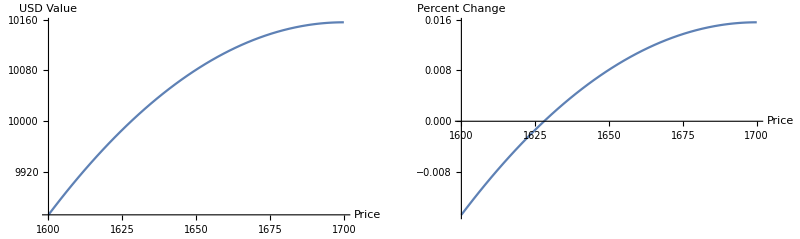

```mathematica
GraphicsGrid[{{
Plot[valueCurve /. { lower -> lowerBound, higher -> upperBound , startPrice -> currentPrice}, {p, lowerBound, upperBound}, AxesLabel->{"Price", "USD Value"}],
Plot[IL /. { lower -> lowerBound, higher -> upperBound , startPrice -> currentPrice}, {p, lowerBound, upperBound},  AxesLabel->{"Price", "Percent Change"}]
}}]
```

#### Closed Form Analysis

```mathematica
procPVOpen = TransformedProcess[currentValue /. {p -> p[t]},p \[Distributed] GeometricBrownianMotionProcess[μ, σ, S],
t]
```

TransformedProcess[L (-√lower+√p[t])+(L (√higher-√p[t]) √p[t])/(√higher),p\[Distributed]GeometricBrownianMotionProcess[μ,σ,S],t]

```mathematica
TableForm[{
{"Mean Function", Mean[procPVOpen[t]] /. {higher -> Subscript[p, b], lower -> Subscript[p, a]}},
{"Variance", Variance[procPVOpen[t]]/. {higher -> Subscript[p, b], lower -> Subscript[p, a]}}
}]
```

Mean Function | L (2 ⅇ^(1/8 t (4 μ-σ^2)) √S-√p_a-(ⅇ^(t μ) S)/(√p_b))
Variance | (ⅇ^(t μ) L^2 S (-ⅇ^(t μ) S+ⅇ^(t (μ+σ^2)) S+(4-4 ⅇ^(-(t σ^2)/4)) p_b+4 ⅇ^(1/8 t (4 μ-σ^2)) √(S p_b)-4 ⅇ^(1/8 t (4 μ+3 σ^2)) √(S p_b)))/p_b

```mathematica
ILOpen =MVIto@@{IL, {p, t},{(diffGBM /. {S-> p})} } // 
Expand //
(# /. {(ⅆt)^2 -> 0, (ⅆW)^2 -> ⅆt , ⅆt ⅆW -> 0} ) &// 
Simplify
procILOpen = ItoProcess[ (ⅆV[t] == IL /. {p -> p[t]}),{V[t]}, {V, Subscript[V, 0]},{t, 0},{ W \[Distributed] WienerProcess[], p \[Distributed] GeometricBrownianMotionProcess[μ, σ, S]}];
TableForm[{
{"Mean Function", Mean[procILOpen[t]] /. {higher -> Subscript[p, b], lower -> Subscript[p, a], startPrice -> Subscript[p, 0]}},
{"Variance", Variance[procILOpen[t]]/. {higher -> Subscript[p, b], lower -> Subscript[p, a],startPrice -> Subscript[p, 0]}}
}]
```

((2 p (2 μ+σ^2)-√higher √p (4 μ+σ^2)) ⅆt+(-4 √higher √p σ+4 p σ) ⅆW)/(4 (√higher (√lower-2 √startPrice)+startPrice))

Mean Function | V_0
Variance | 0

#### Pricing With IL

```mathematica
resultIL =MVIto@@{IL, {p, t},{(diffGBM /. {S-> p})} } // 
Expand //
(# /. {(ⅆt)^2 -> 0, (ⅆW)^2 -> ⅆt , ⅆt ⅆW -> 0} ) &// 
Simplify;
resultIL /. humanReadable
```

(ⅆW (4 p σ-4 √p σ √p_b)+ⅆt (2 p (2 μ+σ^2)-√p (4 μ+σ^2) √p_b))/(4 (p_0+(-2 √p_0+√p_a) √p_b))

```mathematica
preprocessIL = resultIL /. currentLiquidityParams[[1]]/. 
{p -> p[t], W -> W[t],lower -> lowerBound, higher -> upperBound ,μ -> ethMeanYearly/365, σ -> ethDailyVol, startPrice -> currentPrice} // N // Simplify
```

0.000228404 ⅆt √p[t]+0.0028049 ⅆW[t] √p[t]-5.59742×10^-6 ⅆt p[t]-0.0000680288 ⅆW[t] p[t]

```mathematica
procIL = ItoProcess[ ⅆV[t] == preprocessIL,V[t], {V,10000}, {t, 0},{ W \[Distributed] WienerProcess[], p \[Distributed] GeometricBrownianMotionProcess[ethMeanYearly/365, ethDailyVol, currentPrice]}];
fsIL = RandomFunction[procIL, {0, 90}, 5];
```

```mathematica
Mean[fsIL[90]]
```

10000.

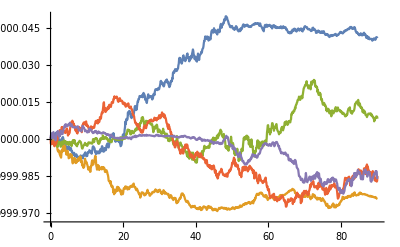

```mathematica
Show[{
ListLinePlot[fsIL, FillingStyle->Axis]
}]
```

#### Pricing with Position Value

```mathematica
preprocessPV = currentValue /. {lower -> lowerBound, higher -> upperBound , p -> p[t]} /. currentLiquidityParams;
```

```mathematica
preprocessPV
```

{8249.71 (-40+√p[t])+200.085 (10 √17-√p[t]) √p[t]}

```mathematica
procPV = TransformedProcess[preprocessPV,{ p \[Distributed] GeometricBrownianMotionProcess[ethMeanYearly/365, ethDailyVol, currentPrice]},
t];
fsPV = RandomFunction[procPV, {0, 90,1}, 5];
```

```mathematica
Mean[fsPV[90]]
```

10038.3

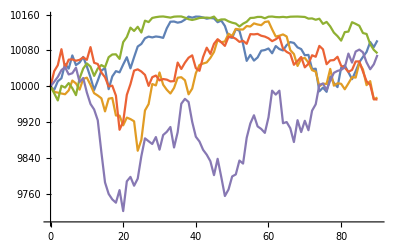

```mathematica
ListLinePlot[fsPV, FillingStyle->Axis]
```

## Further Research

```mathematica
TableForm[{
{"Impermanent Loss in Uniswap V3", Hyperlink["https://lambert-guillaume.medium.com/an-analysis-of-the-expected-value-of-the-impermanent-loss-in-uniswap-bfbfebbefed2"]},
{"Uniswap Liquidity V3 Math", Hyperlink["http://atiselsts.github.io/pdfs/uniswap-v3-liquidity-math.pdf"]}
}]
```

Impermanent Loss in Uniswap V3 | https://lambert-guillaume.medium.com/an-analysis-of-the-expected-value-of-the-impermanent-loss-in-uniswap-bfbfebbefed2
Uniswap Liquidity V3 Math | http://atiselsts.github.io/pdfs/uniswap-v3-liquidity-math.pdf

## Perpetual Lending Stochastic Analysis

## Mean-Reverting Additional Value Term

TBD